## ShowEdgeNormal-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (2.3.6 (9-Nov-2012)) loaded Fri 9 Nov 2012 16:57:06
using xCellerator 0.90 and XSSA 1204002
GPL License Terms Apply

```mathematica
poly={{0,0}, {1,0}, {5,1}, {1, 3}};
```

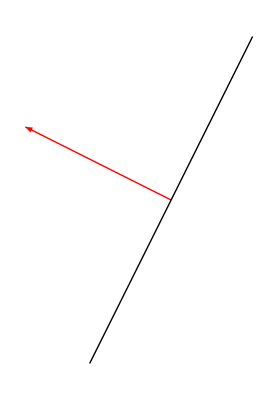

```mathematica
ShowEdgeNormal[{{1,1}, {2,3}}, {Red, Thick}, True]
```

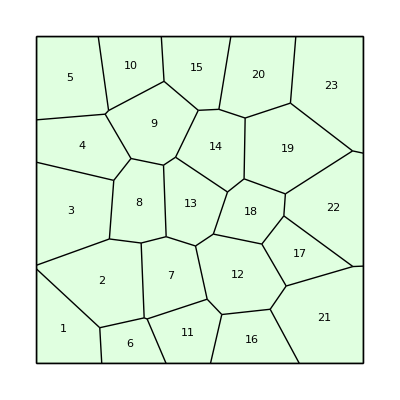

```mathematica
T=TemplateRandomSquareGrid[25, {0,0}, {10,10}];
ShowTissue[T, "CellNumbers"-> True]
```

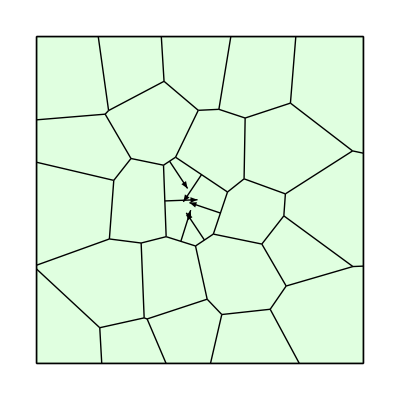

```mathematica
Show[
ShowTissue[T], 
ShowEdgeNormal/@Partition[CellVertexCoordinates[T,13], 2,1,1]
]
```

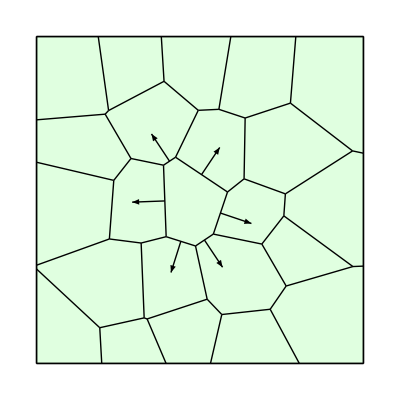

```mathematica
Show[
ShowTissue[T], 
ShowEdgeNormal/@Partition[Reverse[CellVertexCoordinates[T,13]], 2,1,1]
]
```